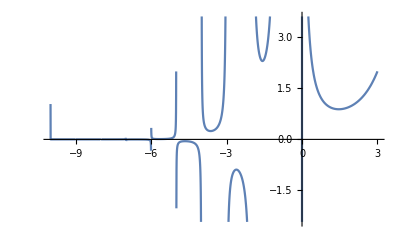

```mathematica
Plot[Gamma[x],{x,-10,3}]
```

```mathematica
Residue[Gamma[x],{x,-10,0}]
```

Residue[Gamma[x],{x,-10,0}]

```mathematica
？Residue
```

？ Residue

```mathematica
Residue[f[z]/z^5,{z,0}]
```

1/24 f^(4)[0]

```mathematica
Table[Residue[Gamma[z],{z,n}],{n,-10,2,1}]
```

{1/3628800,-1/362880,1/40320,-1/5040,1/720,-1/120,1/24,-1/6,1/2,-1,1,0,0}

```mathematica
Plot3D[Abs[Gamma[x+I y]],{x,-3,3},{y,-0.5,0.5}]
```

-Graphics3D-

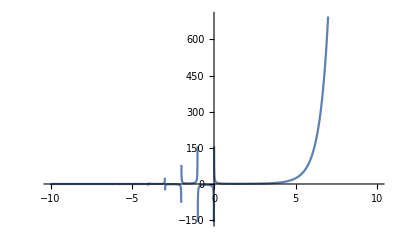

```mathematica
Plot[Gamma[x],{x,-10,10}]
```

```mathematica
Series[Sin[x]/x,{x,0}]
```

Series::sspec: Series specification {x,0} is not a list with three elements.

```mathematica
Series[Sin[x]/x,{x,0,10}]
```

1-x^2/6+x^4/120-x^6/5040+x^8/362880-x^10/39916800+O[x]^11

```mathematica
Integrate[1/(x^2+1),{x,-Infinity,Infinity}]
```

π

Integrate::idiv: Integral of 1/(-1 + x)^4 does not converge on {0, ∞}.

```mathematica
Integrate[Gamma[x],{x,-Infinity,Infinity}]
```

Integrate::idiv: Integral of Gamma[x] does not converge on {-∞,∞}.

∫_(-∞)^∞ Gamma[x]ⅆx

```mathematica
Residue[1/x,{x,0}]
```

1

```mathematica
Residue[1/x,{x,ComplexInfinity}]
```

-1

```mathematica
Residue[Gamma[x],{x,ComplexInfinity}]
```

Residue[Gamma[x],{x,ComplexInfinity}]